```mathematica
Clear["Global`*"]
```

# DE Remainder

## Cory Aitchison - February 2022

Consider how the remainder to the DE looks at different substitutions and A,B values

## Set Up

### Miscellaneous

```mathematica
CC[x_]:=Cos[σ x] / Cosh[σ x];
SS[x_]:=Sin[σ x] / Sinh[σ x];
LDE[f_]:=D[f[x],{x,4}] + 4 σ^4 f[x] ;
NDE[f_]:=Γ f[x]^3;
letters = {c, d, e, f, g, h, i, j, k};
```

### Ansatz

```mathematica
u[n_]:=x|->Sum[letters[[n]][i]CC[x]^((2n+1)-i) SS[x]^(i), {i, 0, 2n+1}];
u[0] := x |->A CC[x] + B SS[x];
```

```mathematica
<<"/Users/cory/Sync/USYD/Denison/Mathematica/PQSHelper.wl"
```

### Solutions

```mathematica
SubAnswers[eq_, n_] := SubAnswers[eq /. answer[n-1], n-1];
SubAnswers[eq_, 1] := eq;

GetEquation[n_]:= LDE[x |-> Sum[u[k][x], {k, 0, n}]] + NDE[x |-> Sum[u[k][x], {k, 0, n-1}]];
GetSolution[n_] := AnalyticSolve[SubAnswers[GetEquation[n], n], n, x, σ, letters[[n]]] // FullSimplify;

GetLinear[ans_] := Coefficient[(Last /@List @@@ ans)/. B->0 ,A, 1]A + Coefficient[(Last /@List @@@ ans)/. A->0 ,B, 1]B;
ShowLinear[n_]:=(x |-> PadRight[x, 2 + 2n,  _])/@GetLinear/@ (answer[#]&/@Range[1,n]) // Transpose// MatrixForm ;

ShowValues[n_] := (x |-> PadRight[x, 2 + 2n, _])/@((answer[#]/. param /. estimates)&/@Range[1,n])//Transpose//MatrixForm;

FinalFunction[n_] := SubAnswers[Sum[u[k][x], {k, 0, n}], n+1]/.param  /. estimates;
FinalFunction[0] := u[0][x] /. param /. estimates;
```

### Numerical Values

```mathematica
param = {σ-> 6^(1/4), Γ -> -24};
estimates = {A -> 0.445408, B -> 1.02817};
flatests = {A->0.242423,B->0.898534};
taylorests[0] = {A->0.033327514775158475,B->1.153359200278144};
taylorests[1] = {A->0.24242264239512362,B->0.8985343791605391};
taylorests[3] = {A->0.33494186742400267,B->0.6945601303275413};
```

```mathematica
DumpGet["/Users/cory/Sync/USYD/Denison/Mathematica/answerSave.mx"]
```

## Remainder Plots

```mathematica
f[x_]:= SubAnswers[u[1][x] + u[0][x], 2];
g[x_]:=SubAnswers[u[2][x] + u[1][x] + u[0][x], 3];
ff[n_]:= x|->SubAnswers[Sum[u[k][x], {k, 0, n}], n+1];de[f_]:=x|->(D[f[t], {t,4}] /. t->x)+ 4 σ^4 f[x] + Γ f[x]^3;
```

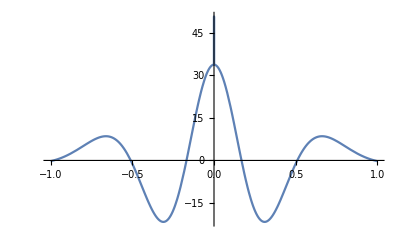

```mathematica
Plot[de[ff[1]][x] /. param /. estimates, {x, -1, 1}]
```

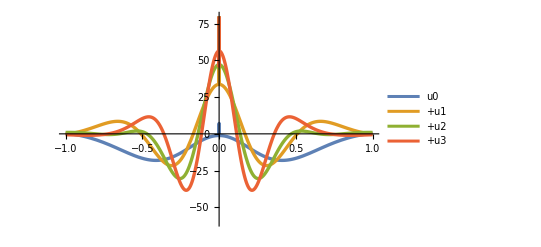

```mathematica
Plot[{
de[ff[0]][x] /. param /. estimates,
de[ff[1]][x] /. param /. estimates,
de[ff[2]][x] /. param /. estimates,
de[ff[3]][x] /. param /. estimates
}, {x,-1,1},PlotLegends-> {"u0", "+u1", "+u2", "+u3"}, PlotStyle->{Thickness[0.006]}, PlotRange->{Automatic, {-60, 80}}]
```

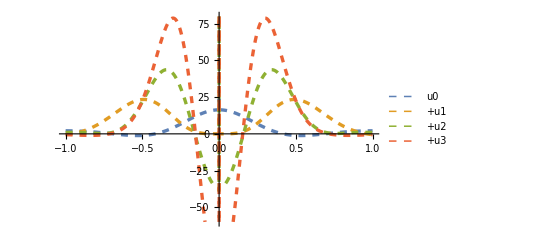

```mathematica
Plot[{
de[ff[0]][x] /. param /. flatests,
de[ff[1]][x] /. param /. flatests,
de[ff[2]][x] /. param /. flatests,
de[ff[3]][x] /. param /. flatests
}, {x,-1,1},PlotLegends-> {"u0", "+u1", "+u2", "+u3"}, PlotStyle->{{Thickness[0.006], Dashed}, {Thickness[0.006], Dashed}}, PlotRange->{Automatic, {-60, 80}}]
```

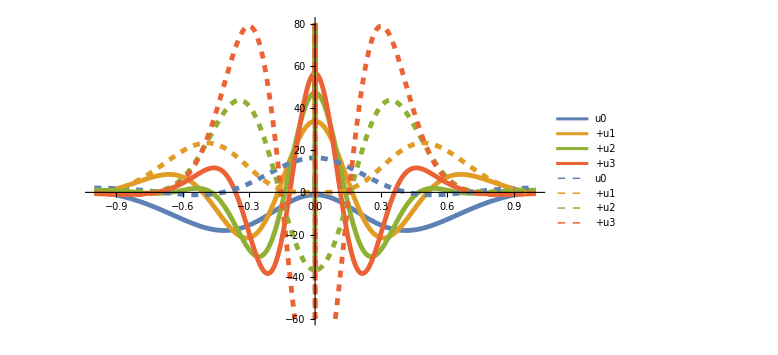

```mathematica
Show[%1006, %1005]
```

Recalculate A,B for the other dashed curves

```mathematica
Series[de[ff[0]][x], x -> 0] /. estimates /. param
```

-1.13398+O[x]^2

### Using the correct Taylor values

Use the appropriate Taylor values so that it is 0 at the origin for the dashed curves

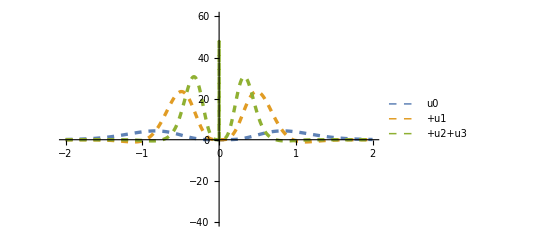

```mathematica
Plot[{
de[ff[0]][x] /. param /. taylorests[0],
de[ff[1]][x] /. param /. taylorests[1],
de[ff[3]][x] /. param /. taylorests[3]
}, {x,-2,2},PlotLegends-> {"u0", "+u1", "+u2+u3"}, PlotStyle->{{Thickness[0.006], Dashed}, {Thickness[0.006], Dashed}}, PlotRange->{Automatic, {-40, 60}}]
```

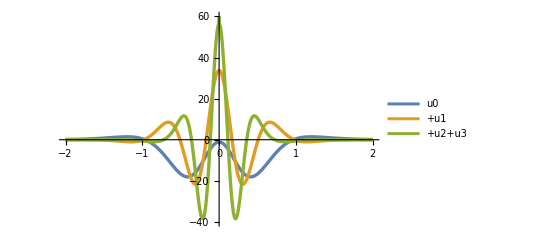

```mathematica
Plot[{
de[ff[0]][x] /. param /. estimates,
de[ff[1]][x] /. param /. estimates,
de[ff[3]][x] /. param /. estimates
}, {x,-2,2},PlotLegends-> {"u0", "+u1", "+u2+u3"}, PlotStyle->{Thickness[0.006]}, PlotRange->{Automatic, {-40, 60}}]
```

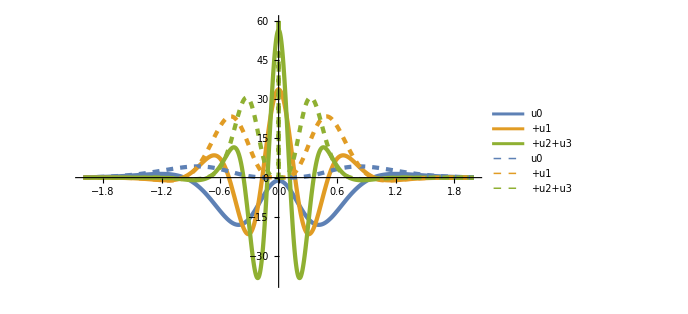

```mathematica
Show[%1145, %1144]
```

## Contributions

What are the contributions from the three components of the DE?

```mathematica
de1[f_]:=x|->(D[f[t], {t,4}] /. t->x);
de2[f_]:=x |-> 4 σ^4 f[x];
de3[f_]:=x|-> Γ f[x]^3;
```

### Visual estimates

Using A, B from the visual estimates.

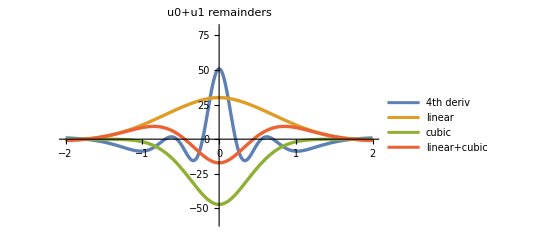

```mathematica
Plot[{
de1[ff[1]][x] /. param /. estimates,
de2[ff[1]][x] /. param /. estimates,
de3[ff[1]][x] /. param /. estimates,
de2[ff[1]][x] + de3[ff[1]][x] /. param /. estimates
}, {x,-2,2},PlotLegends-> {"4th deriv", "linear", "cubic","linear+cubic"}, PlotStyle->{Thickness[0.006]}, PlotRange->{Automatic, {-60, 80}}, PlotLabel->"u0+u1 remainders"]
```

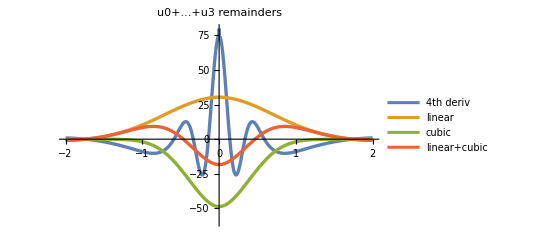

```mathematica
Plot[{
de1[ff[3]][x] /. param /. estimates,
de2[ff[3]][x] /. param /. estimates,
de3[ff[3]][x] /. param /. estimates,
de2[ff[3]][x] + de3[ff[3]][x] /. param /. estimates
}, {x,-2,2},PlotLegends-> {"4th deriv", "linear", "cubic", "linear+cubic"}, PlotStyle->{Thickness[0.006]}, PlotRange->{Automatic, {-60, 80}}, PlotLabel->"u0+...+u3 remainders"]
```

### Taylor estimates

Using the taylor expansion estimates

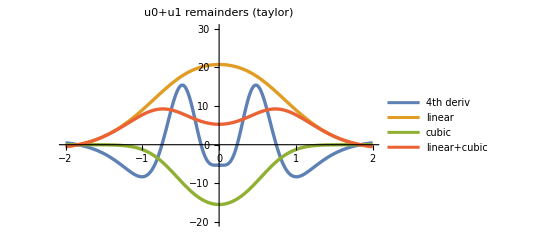

```mathematica
Plot[{
de1[ff[1]][x] /. param /. taylorests[1],
de2[ff[1]][x] /. param /. taylorests[1],
de3[ff[1]][x] /. param /. taylorests[1],
de2[ff[1]][x] + de3[ff[1]][x] /. param /. taylorests[1]
}, {x,-2,2},PlotLegends-> {"4th deriv", "linear", "cubic","linear+cubic"}, PlotStyle->{Thickness[0.006]}, PlotRange->{Automatic, {-20, 30}}, PlotLabel->"u0+u1 remainders (taylor)"]
```

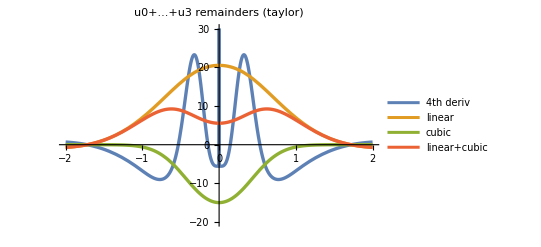

```mathematica
Plot[{
de1[ff[3]][x] /. param /. taylorests[3],
de2[ff[3]][x] /. param /. taylorests[3],
de3[ff[3]][x] /. param /. taylorests[3],
de2[ff[3]][x] + de3[ff[3]][x] /. param /. taylorests[3]
}, {x,-2,2},PlotLegends-> {"4th deriv", "linear", "cubic", "linear+cubic"}, PlotStyle->{Thickness[0.006]}, PlotRange->{Automatic, {-20, 30}}, PlotLabel->"u0+...+u3 remainders (taylor)"]
```

# Test

```mathematica
data = Import["/Users/cory/Sync/USYD/Denison/MATLAB/PQS analytic/PureQuartic.csv"];
```

```mathematica
m[x_]:=a1 (Cos[x σ]Sech[x σ] + Sin[x σ] Sinh[x σ]) (1 - Exp[-σ x^2]) / (1 + Exp[-σ x^2]) + a2 Exp[-σ x^2];
```

```mathematica
m[x]
```

a2 ⅇ^(-x^2)+(a1 (1-ⅇ^(-x^2 σ)) (Cos[x σ] Sech[x σ]+Sin[x σ] Sinh[x σ]))/(1+ⅇ^(-x^2 σ))

```mathematica
Manipulate[Show[Plot[m[x] /. param /. {a1 -> aa1, a2 -> aa2}, {x,-2,2}], ListLinePlot[Transpose[{data[[;;,1]], data[[;;,2]]}], PlotStyle->{{Orange, Thick}}, PlotRange->{{-2,2}, {0, 2}}, PlotLegends->{"Data"}]], {aa1, 0, 2}, {aa2, 0, 2}]
```

ReplaceAll::reps: {param} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ReplaceAll::reps: {param} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.